```mathematica
(*Cosmomathica version 0.2, February 2014. By Adrian Vollmer, Institute for theoretical physics, University Heidelberg.*)
```

## Preamble

```mathematica
BeginPackage["cosmomathica`interface`"]
```

cosmomathica`interface`

```mathematica
Transfer::usage="Transfer[OmegaM, fBaryon, Tcmb, h] provides an interface to Eisenstein & Hu's fitting formula for the transfer function. It takes the reduced total matter density Ω_M, the fraction of baryons Ω_b/Ω_M, the CMB temperature and the dimensionless Hubble constant as input, and returns the sound horizon, the wavenumber k_peak where the spectrum has a maximum, the transfer function for CDM, baryons, both, or with no baryons or no wiggles.";

Halofit::usage="Halofit[OmegaM, OmegaL, gammaShape, sigma8, ns, betaP, z0] provides an interface to the halofit algorithm by Robert E. Smith et al. (reimplemented in C by Martin Kilbinger). It takes the total matter density Ω_M, the vacuum energy density Ω_L, a shape factor, σ_8, n_s, β_p, and a fixed redshift z_0 as input, and returns the nonlinear matter power spectrum (computed in three ways: linearly with the BBKS alogorithm, nonlinear with the algorithm by Peacock and Dobbs, or nonlinearly with the Halofit algorithm) at 20 different values of the scale factor and the convergence power spectrum in tabulated form.";

CosmicEmu::usage="CosmicEmu[omegaM, omegaB, sigma8, ns, w] provides an interface to the CosmicEmulator by Earl Lawrence. It takes ω_M, ω_b, σ_8, n_s, and the equation of state w, and returns the nonlinear matter power spectrum at five different redshifts as well as z, H, d (all at last scattering), and the sound horizon.";

FrankenEmu::usage="FrankenEmu[omegaM, omegaB, h, sigma8, ns, w] provides an interface to FrankenEmu by Earl Lawrence. It takes ω_M, ω_b, h, σ_8, n_s, and the equation of state w, and returns the nonlinear matter power spectrum at five different redshifts as well as z, H, d (all at last scattering), and the sound horizon. The Hubble parameter h can also be omitted, in which case it will be determined from the CMB just as in CosmicEmu. Additional cosmological parameters are only returned if h is missing.";

CAMB::usage="CAMB[OmegaC, OmegaB, OmegaL, h, w] provides an interface to CAMB by Antony Lewis and Anthony Challinor. It takes a few parameters as well as a number of options as input, and returns various cosmological quantities. The distinction between parameters and options is in principle arbitrary. However, since some physical parameters are often assumed to take on a default value, they are being interpreted as an option here. To see the default options, type `Options[CAMB]`.";

CLASS::usage="CLASS[\"parameter1\" -> \"value1\",...] runs Class"; 

Copter::usage="Copter[OmegaM, OmegaB, h, ns, sigma8, transfer, z, type] provides an interface to Copter by Jordan Carlson. It takes Ω_M, Ω_b, h, n_s, σ_8, the transfer function in shape of a list of value pairs and returns the power spectrum and other quantities. The 'type' variable specifies which pertubration theory is used and must take one of the following values (as a string): 'SPT' (Standard PT), 'RPT' (Renormalized PT), 'LPT' (Lagrangian PT), 'FWT' (Flowing with time, TRG), 'LargeN', 'HSPT' (Higher order PT), 'NW' (no wiggles, Eisenstein&Hu algorithm), 'Linear'. Several options can be specified.";

CopterGrowth::usage="CopterGrowth[OmegaM, OmegaB, h, ns, z] returns the growth function computed by Copter evaluated at each redshift contained in the list z.";
```

```mathematica
Tcmb::usage="An option for CAMB";
OmegaNu::usage="An option for CAMB";
YHe::usage="An option for CAMB";
MasslessNeutrinos::usage="An option for CAMB";
MassiveNeutrinos::usage="An option for CAMB";
NuMassDegeneracies::usage="An option for CAMB";
NuMassFractions::usage="An option for CAMB";
ScalarInitialCondition::usage="An option for CAMB";
NonLinear::usage="An option for CAMB";
WantCMB::usage="An option for CAMB";
WantTransfer::usage="An option for CAMB";
WantCls::usage="An option for CAMB";
ScalarSpectralIndex::usage="An option for CAMB";
ScalarRunning::usage="An option for CAMB";
TensorSpectralIndex::usage="An option for CAMB";
RatioScalarTensorAmplitudes::usage="An option for CAMB";
ScalarPowerAmplitude::usage="An option for CAMB";
PivotScalar::usage="An option for CAMB";
PivotTensor::usage="An option for CAMB";
DoReionization::usage="An option for CAMB";
UseOpticalDepth::usage="An option for CAMB";
OpticalDepth::usage="An option for CAMB";
ReionizationRedshift::usage="An option for CAMB";
ReionizationFraction::usage="An option for CAMB";
ReionizationDeltaRedshift::usage="An option for CAMB";
TransferHighPrecision::usage="An option for CAMB";
WantScalars::usage="An option for CAMB";
WantVectors::usage="An option for CAMB";
WantTensors::usage="An option for CAMB";
WantZstar::usage="An option for CAMB";
WantZdrag::usage="An option for CAMB";
OutputNormalization::usage="An option for CAMB";
MaxEll::usage="An option for CAMB";
MaxEtaK::usage="An option for CAMB";
MaxEtaKTensor::usage="An option for CAMB";
MaxEllTensor::usage="An option for CAMB";
TransferKmax::usage="An option for CAMB";
TransferKperLogInt::usage="An option for CAMB";
TransferRedshifts::usage="An option for CAMB";
AccuratePolarization::usage="An option for CAMB";
AccurateReionization::usage="An option for CAMB";
AccurateBB::usage="An option for CAMB";
DoLensing::usage="An option for CAMB";
OnlyTransfers::usage="An option for CAMB";
DerivedParameters::usage="An option for CAMB";
MassiveNuMethod::usage="An option for CAMB";
zInitial::usage="Initial redshift for Copter";
Neta::usage = "Number of time steps for Copter";
kcut::usage="Cutoff wavenumber for Copter";
epsrel::usage="Relative error for integration methods for Copter";
qmin::usage="qmin for Copter";
qmax::usage="qmax for Copter";
order::usage="Order for Higher order SPT for Copter";
formula::usage="Equation to use for No-Wiggle spectrum in Copter (must be 1, 2 or 3)";
```

```mathematica
CAMB::Eigenstates="NuMassEigenstates and NuMassFractions must have the same length  (can be zero).";
CAMB::InvalidOption="Option `1` is '`2`', but must be one of the following: `3`";
CAMB::Lists="The following options need to be non-empty lists of the same length: `1`";
CAMB::Error="CAMB exited with the following error code: `1`";
Interface::LinkBroken="`1` crashed. See if there is anything useful on stdout.";
Interface::OutsideBounds="Parameter out of bounds. `5` requires `3` <= `1` <= `4`, but you have `1`=`2`.";
Interface::NotInstalled="`1` appears to be unavailable on your system.";
Interface::MathLinkFail="The MathLink failed. Check if there is anything useful on stdout.";
Copter::InvalidType="Type is '`1`', but must be one of the following: `2`";
CLASS::Error="`1` => `2`";
```

## Main

```mathematica
Begin["`Private`"]
```

cosmomathica`interface`Private`

```mathematica
$location=DirectoryName[$InputFileName];
```

```mathematica
bool2int[b_]:=If[b,1,0];
validatestring[val_,name_,poss_]:=If[!MemberQ[poss,val],Message[CAMB::InvalidOption,name,val,StringJoin@@Riffle[poss,", "]];Abort[]];
validatelimits[val_,name_,lower_,upper_,module_]:=If[!(lower≤val≤upper),Message[Interface::OutsideBounds,name,val,lower,upper,module];Abort[]];
validatelists[list_]:=If[1!=Length@Union[Length/@list],Message[CAMB::Lists,list];Abort[]];
validateresult[x_,name_]:=Switch[x,$Failed,Message[Interface::LinkBroken,name];Abort[];False,Null,Message[Interface::NotInstalled,name]False,_,True];
```

```mathematica
reshape[list_,dimensions_]:=First[Fold[Partition[#1,#2]&,Flatten[list],Reverse[dimensions]]]
```

### CLASS

```mathematica
CLASS[options:OptionsPattern[]]:=Module[{link,inifile,tempdir,result,s,limits},
tempdir=CreateDirectory[];
inifile=tempdir<>"/mathematica.ini";
Export[inifile,Table[o[[1]]<>" = "<>o[[2]],{o,{options}}]~Join~{"root = "<>tempdir<>"/out_"},"Text"];

link=Install[$location<>"ext/math_link"];
result=Global`Class[inifile];
validateresult[result,"CLASS"];
Uninstall[link];
DeleteDirectory[tempdir,DeleteContents->True];

If[And@@StringQ/@result,Message[CLASS::Error,result[[1]],result[[2]]];Return[$Failed];Abort[]];
limits=Select[First@result,#≠0&]/.{-1->"kvalues",-2->"tauvalues",-3->"sigma8",-4->"transfer",-5->"linearPk"};
limits=Partition[limits,2];

Table[
With[{count=If[i==1,0,Total@limits[[;;i-1,2]]]},
CLASS[limits[[i,1]]]->result[[2,count+1;;count+limits[[i,2]]]]],
{i,Length@limits}]
];
```

### CAMB

```mathematica
CAMB[OmegaC_?NumericQ,OmegaB_?NumericQ,OmegaL_?NumericQ,h_?NumericQ,w_?NumericQ,opts:OptionsPattern[]]:=Module[{j,link,result,resultfloat,resultint,floats,ints,initialcond,nonlinear,massivenu,limits,check,getDimensions,dimensions,array,redshifts},

getDimensions[list_]:=Module[{i,r},
i=1;r={};
While[i<Length@list,AppendTo[r,list[[i+1;;i+list[[i]]]]];i=i+1+list[[i]]];
r];


(*some parameters must be within certain limits*)
limits={{ReionizationFraction,0,1.5},
{OpticalDepth,0,.9},
{h,"h",.2,1.},
{Tcmb,2.7,2.8},
{YHe,.2,.8},
{MasslessNeutrinos,0,3.1},
(*MassiveNeutrinos?*)
{OmegaB,"Ω_B",.001/h^2,1./h^2},
{OmegaC ,"Ω_C",0./h^2,3./h^2}
};


validatelists[OptionValue@{ScalarSpectralIndex,ScalarRunning,TensorSpectralIndex,RatioScalarTensorAmplitudes,ScalarPowerAmplitude}];
validatelists[OptionValue@{NuMassDegeneracies,NuMassFractions}];
validatelimits[Sequence@@If[NumericQ[#[[1]]],#,{OptionValue[#[[1]]],ToString[#[[1]]]}~Join~Rest@#],"CAMB"]&/@limits;

initialcond={"vector","adiabatic","iso_CDM","iso_baryon","iso_neutrino","iso_neutrino_vel"};
nonlinear={"none","pk","lens","both"};
massivenu={"int","trunc","approx","best"};

validatestring[OptionValue[ScalarInitialCondition],"ScalarInitialCondition",initialcond];
validatestring[OptionValue[NonLinear],"NonLinear",nonlinear];
validatestring[OptionValue[MassiveNuMethod],"MassiveNuMethod",massivenu];

floats=Flatten@{OmegaC,OmegaB,OmegaL,h*100,OptionValue[#]&/@{OmegaNu,Tcmb,YHe,MasslessNeutrinos,NuMassDegeneracies,NuMassFractions,ScalarSpectralIndex,ScalarRunning,TensorSpectralIndex,RatioScalarTensorAmplitudes,ScalarPowerAmplitude,PivotScalar,PivotTensor,OpticalDepth,ReionizationRedshift,ReionizationFraction,ReionizationDeltaRedshift,MaxEtaK,MaxEtaKTensor,TransferKmax},Reverse@Sort@OptionValue@TransferRedshifts};

ints=Flatten@{OptionValue[MassiveNeutrinos],Length@OptionValue[NuMassFractions],Position[initialcond,OptionValue[ScalarInitialCondition]][[1,1]]-1,Position[nonlinear,OptionValue[NonLinear]][[1,1]]-1,Length@OptionValue@ScalarSpectralIndex,bool2int/@OptionValue@{DoReionization,UseOpticalDepth,TransferHighPrecision,WantCMB,WantTransfer,WantCls,WantScalars,WantVectors,WantTensors,WantZstar, WantZdrag},OptionValue[#]&/@{OutputNormalization,MaxEll,MaxEllTensor,TransferKperLogInt},Length@OptionValue@TransferRedshifts,bool2int/@OptionValue@{AccuratePolarization,AccurateReionization,AccurateBB,DoLensing,OnlyTransfers,DerivedParameters},Position[massivenu,OptionValue[MassiveNuMethod]][[1,1]]-1};

(*Print[ints,floats];*)
SetDirectory[$location<>"ext/camb"];
link=Install[$location<>"ext/math_link"];
result=Global`CAMBrun[N/@floats,ints];
ResetDirectory[];
If[!validateresult[result,"CAMB"],Return[$Failed];Abort[]];
Uninstall[link];

{resultfloat,resultint}=result;
If[resultint[[1]]≠0,Message[CAMB::Error,resultint[[1]]];Return[$Failed];Abort[]];
resultint=Drop[resultint,1];
dimensions=getDimensions@resultint;

Do[array=Take[resultfloat,Times@@d];
resultfloat=Drop[resultfloat,Times@@d];
AppendTo[resultfloat,reshape[array,d]],{d,dimensions}];

j=2;
DeleteCases[{
CAMB["age"]->resultfloat[[1,1]],
CAMB["zstar"]->resultfloat[[1,2]],
CAMB["rstar"]->resultfloat[[1,3]],
CAMB["100thetastar"]->resultfloat[[1,4]],
CAMB["zdrag"]->resultfloat[[1,5]],
CAMB["rdrag"]->resultfloat[[1,6]],
CAMB["kD"]->resultfloat[[1,7]],
CAMB["100thetaD"]->resultfloat[[1,8]],
CAMB["zEQ"]->resultfloat[[1,9]],
CAMB["100thetaEQ"]->resultfloat[[1,10]],
CAMB["sigma8"]->resultfloat[[-1]],
If[OptionValue[WantScalars],CAMB["CLscalar"]->Transpose@First@Transpose[resultfloat[[j++]]]],
If[OptionValue[WantVectors],CAMB["CLvector"]->Transpose@First@Transpose[resultfloat[[j++]]]],
If[OptionValue[WantTensors],CAMB["CLtensor"]->Transpose@First@Transpose[resultfloat[[j++]]]],
If[OptionValue[WantTransfer],CAMB["redshifts"]->(redshifts=resultfloat[[-2]])],
If[OptionValue[WantTransfer],Sequence@@Flatten@{
CAMB["PSlinear"]->Table[Exp@Transpose@{resultfloat[[j]],resultfloat[[j+1,All,k]]},{k,Length@redshifts}],
CAMB["PSnonlinear"]->Table[Exp@Transpose@{resultfloat[[j]],resultfloat[[j+2,All,k]]},{k,Length@redshifts}
]}~Join~{CAMB["Transfer"]->Table[Transpose[resultfloat[[j+3,All,All,k]]],{k,Length@redshifts}]}
](*,CAMB["ints"]->resultint,CAMB["floats"]->resultfloat*)
},Null]
];
Options[CAMB]={Tcmb->2.7255,OmegaNu->0,YHe->.24,MasslessNeutrinos->3.046,MassiveNeutrinos->0,NuMassDegeneracies->{0},NuMassFractions->{1},ScalarInitialCondition->"adiabatic",NonLinear->"none",WantCMB->True,WantTransfer->True,WantCls->True,ScalarSpectralIndex->{.96},ScalarRunning->{0},TensorSpectralIndex->{0},RatioScalarTensorAmplitudes->{1},ScalarPowerAmplitude->{2.1*^-9},PivotScalar->.05,PivotTensor->.05,DoReionization->True,UseOpticalDepth->False,OpticalDepth->0.,ReionizationRedshift->10.,ReionizationFraction->1.,ReionizationDeltaRedshift->.5,TransferHighPrecision->False,WantScalars->True,WantVectors->True,WantTensors->True,WantZstar->True, WantZdrag->True,OutputNormalization->1,MaxEll->1500,MaxEtaK->3000.,MaxEtaKTensor->800.,MaxEllTensor->400,TransferKmax->.9,TransferKperLogInt->0,TransferRedshifts->{0.},AccuratePolarization->True,AccurateReionization->False,AccurateBB->False,DoLensing->True,OnlyTransfers->False,DerivedParameters->True,MassiveNuMethod->"best"};
Options[validatestring]=Options[CAMB];
```

### Transfer

```mathematica
(*Transfer function*)
Transfer[OmegaM_?NumericQ,fBaryon_?NumericQ,Tcmb_?NumericQ,h_?NumericQ]:=Module[{result,link,krange,fitonek,horizon,peak,OmegaC},
validatelimits[fBaryon,"fBaryon",.0001,1,"Transfer"];
OmegaC=OmegaM-fBaryon*OmegaM;
link=Install[$location<>"ext/math_link"];

(*These random factors of h are ridiculous. Read the comments in the source (tf.c) very carefully*)
Global`TFSetParameters[N@OmegaM*h^2,N@fBaryon,N@Tcmb];
horizon=Global`TFSoundHorizon[N@OmegaM,N@fBaryon,N@h];
peak=Global`TFkPeak[N@OmegaM,N@fBaryon,N@h];
If[!validateresult[horizon,"transfer"],Return[$Failed];Abort[]];

fitonek[k_]:=Join[Global`TFFitOneK[k*N@h],{
Global`TFNoWiggles[N@OmegaM,N@fBaryon,N@h,N@Tcmb,k],
Global`TFZeroBaryon[N@OmegaM,N@h,N@Tcmb,k]}]; 
krange=10^Range[-6.,4.,.01];
result=Transpose[fitonek/@krange];
Uninstall[link];

{Transfer["soundhorizon"]->horizon,
Transfer["peak"]->peak,
Transfer["kvalues"]->krange,
Transfer["full"]->result[[1]],
Transfer["baryon"]->result[[2]],
Transfer["cdm"]->result[[3]],
Transfer["nowiggles"]->result[[4]],
Transfer["zerobaryons"]->result[[5]]}
];
```

### Halofit

```mathematica
Halofit[OmegaM_?NumericQ,OmegaL_?NumericQ,gammaShape_?NumericQ,sigma8_?NumericQ,ns_?NumericQ,betaP_?NumericQ,z0_?NumericQ]:=Module[{link,Tf={},Kappa={},arange,krange,ellrange,labels,limits,parameters,check},
link=Install[$location<>"ext/math_link"];

arange=Most[10^Range[-2,0,.1]]~Join~{.99999};
krange=10^Range[-4,4,.1]*2998;(*halofit uses units c Mpc/h*)
ellrange=10^Range[-2,6,.1];

labels={"Ω_M","Ω_b","σ_8","n_s","Gamma","β_p","z_0"};
limits={{.1,1.5},{.1,1.5},{.1,1.5},{.7,1.3},{0.05,.5},{1.0,2.0},{.2,1.5}};
(*these are soft limits as given by the authors of halofit+. Results may not be reliable if parameters are outside these bounds*)
parameters={OmegaM,OmegaL,sigma8,ns,gammaShape,betaP,z0};

check=(#[[2,1]]<=#[[1]]<=#[[2,2]])&/@Transpose[{parameters,limits}];
Do[If[!check[[i]],Message[Interface::OutsideBounds,labels[[i]],parameters[[i]],limits[[i,1]],limits[[i,2]],"Halofit"]],{i,Length@check}];
If[!And@@check,Abort[]];


Do[
Global`HFSetParameters[N@OmegaM,N@OmegaL,N@gammaShape,N@sigma8,N@ns,N@betaP,N@z0,i];
AppendTo[Tf,Table[Global`HFGetPkNL[a,k],{a,arange},{k,krange}]];
AppendTo[Kappa,Table[Global`HFGetKappa[ell],{ell,ellrange}]],
{i,0,2}];
validateresult[Global`HFGetKappa[10.],"halofit"];
Uninstall[link];

arange[[-1]]=1.;
(*Just return the raw numbers*)
{Halofit["avalues"]->arange,
Halofit["kvalues"]->krange,
Halofit["ellvalues"]->ellrange,
Halofit["kappaBBKS"]->Kappa[[1]],Halofit["BBKS"]->Tf[[1]],
Halofit["kappaPD96"]->Kappa[[2]],Halofit["PD96"]->Tf[[2]],
Halofit["kappaHalofit"]->Kappa[[3]],Halofit["Halofit"]->Tf[[3]]}
];
```

### CosmicEmu

```mathematica
CosmicEmu[omegaM_?NumericQ,omegaB_?NumericQ,sigma8_?NumericQ,ns_?NumericQ,w_?NumericQ]:=Module[{link,result,labels,limits,parameters,check,arange},

labels={"ω_M","ω_b","σ_8","n_s","w"};
limits={{.12,.155},{.0214,.0235},{.61,.9},{.85,1.05},{-1.3,-.7}};
(*these are hard limits as given by the authors of the cosmic emulator - the program will crash if any parameter is outside its bounds*)
parameters={omegaM,omegaB,sigma8,ns,w};
arange=Range[.5,1.,.1];

check=(#[[2,1]]<=#[[1]]<=#[[2,2]])&/@Transpose[{parameters,limits}];
Do[If[!check[[i]],Message[Interface::OutsideBounds,labels[[i]],parameters[[i]],limits[[i,1]],limits[[i,2]],"CosmicEmu"]],{i,Length@check}];
If[!And@@check,Abort[]];

link=Install[$location<>"ext/math_link"];
result=Table[{Transpose@Partition[#[[1]],Length@#[[1]]/2],#[[2]]}&@Global`CEGetPkNL[N@omegaM,N@omegaB,N@ns,N@sigma8,N@w,1/a-1],{a,arange}];
 (*CosmicEmu only does these five redshifts, everything else is interpolated*)
validateresult[(result[[All,2]])[[1,4]],"CosmicEmu"];
Uninstall[link];

(*Just return the raw numbers*)
{CosmicEmu["zvalues"]->Table[1/a-1,{a,arange}],
CosmicEmu["pk"]->result[[All,1]],
CosmicEmu["soundhorizon"]->(result[[All,2]])[[1,1]],
CosmicEmu["zlss"]->(result[[All,2]])[[1,2]],
CosmicEmu["dlss"]->(result[[All,2]])[[1,3]],
CosmicEmu["hubblecmb"]->(result[[All,2]])[[1,4]]}
];
```

### FrankenEmu

```mathematica
FrankenEmu[omegaM_?NumericQ,omegaB_?NumericQ,h_?NumericQ,sigma8_?NumericQ,ns_?NumericQ,w_?NumericQ]:=Module[
{link,result,labels,limits,parameters,check, arange},

arange=Range[.2,1.,.1];
labels={"ω_M","ω_b","σ_8","n_s","w","h"};
limits={{.12,.155},{.0215,.0235},{.6,.9},{.85,1.05},{-1.3,-.7},{.55,.85}};
(*these are hard limits as given by the authors of the cosmic emulator - the program will crash if any parameter is outside its bounds*)
parameters={omegaM,omegaB,sigma8,ns,w,If[h<0,.7,h]};

check=(#[[2,1]]<=#[[1]]<=#[[2,2]])&/@Transpose[{parameters,limits}];
Do[If[!check[[i]],Message[Interface::OutsideBounds,labels[[i]],parameters[[i]],limits[[i,1]],limits[[i,2]],"FrankenEmu"]],{i,Length@check}];
If[!And@@check,Abort[]];

link=Install[$location<>"ext/math_link2"];
result=Table[{Transpose@Partition[#[[1]],Length@#[[1]]/2],#[[2]]}&@Global`FrankenCEGetPkNL[N@omegaM,N@omegaB,N@h,N@ns,N@sigma8,N@w,1/a-1],{a,arange}];
 (*CosmicEmu only does these five redshifts, everything else is interpolated*)
validateresult[(result[[1,1]]),"FrankenEmu"];
Uninstall[link];

(*Just return the raw numbers*)
{FrankenEmu["zvalues"]->Table[1/a-1,{a,arange}],
FrankenEmu["pk"]->result[[All,1]]}~Join~If[h<0,
{FrankenEmu["soundhorizon"]->(result[[All,2]])[[1,1]],
FrankenEmu["zlss"]->(result[[All,2]])[[1,2]],
FrankenEmu["dlss"]->(result[[All,2]])[[1,3]],
FrankenEmu["hubblecmb"]->(result[[All,2]])[[1,4]]},{}]
];
FrankenEmu[omegaM_?NumericQ,omegaB_?NumericQ,sigma8_?NumericQ,ns_?NumericQ,w_?NumericQ]:=FrankenEmu[omegaM,omegaB,-1.,sigma8,ns,w];
```

### Copter

```mathematica
Copter[OmegaM_,OmegaB_,h_,ns_,sigma8_,transfer_,z_,type_,opts:OptionsPattern[]]:=Module[{link,result,return,kmax},
kmax=1.5;
link=Install[$location<>"ext/math_link"];
return=Switch[type,
"RPT",result=Global`CopterRpt[N@h,N@ns,N@OmegaM,N@OmegaB,N@sigma8,N@OptionValue@zInitial,N@z,OptionValue@Neta,N@OptionValue@kcut,N@transfer[[All,1]],N@transfer[[All,2]]];
If[result==$Failed,Message[Interface::MathLinkFail];Return[$Failed];Abort[]];
result=Transpose@Partition[result,3];
{Copter["P11"]->result[[1]],Copter["P12"]->result[[2]],Copter["P22"]->result[[3]]},

"SPT",result=Global`CopterSpt[N@h,N@ns,N@OmegaM,N@OmegaB,N@sigma8,N@z,N@OptionValue@epsrel,N@transfer[[All,1]],N@transfer[[All,2]]];
If[result==$Failed,Message[Interface::MathLinkFail];Return[$Failed];Abort[]];
result=Transpose@Partition[result,4];
{Copter["P11"]->result[[1]],Copter["P12"]->result[[2]],Copter["P22"]->result[[3]],Copter["1L-Propagator"]->result[[4]]},

"LPT",result=Global`CopterLpt[N@h,N@ns,N@OmegaM,N@OmegaB,N@sigma8,N@z,N@OptionValue@epsrel,N@transfer[[All,1]],N@transfer[[All,2]]];
If[result==$Failed,Message[Interface::MathLinkFail];Return[$Failed];Abort[]];
result=Transpose@Partition[result,4];
{Copter["P"]->result[[1]],Copter["P22"]->result[[2]],Copter["P13"]->result[[3]],Copter["1L-Propagator"]->result[[4]]},

"LargeN",result=Global`CopterLargeN[N@h,N@ns,N@OmegaM,N@OmegaB,N@sigma8,N@OptionValue@zInitial,N@z,20,N@OptionValue@epsrel,N@transfer[[All,1]],N@transfer[[All,2]]];
If[result==$Failed,Message[Interface::MathLinkFail];Return[$Failed];Abort[]];
result=Transpose@Partition[result,7];
{Copter["P11"]->result[[1]],Copter["P12"]->result[[2]],Copter["P22"]->result[[3]],Copter["Sigma11"]->result[[4]],Copter["Sigma12"]->result[[5]],Copter["Sigma21"]->result[[6]],Copter["Sigma22"]->result[[7]]},

"HSPT",result=Global`CopterHspt[N@h,N@ns,N@OmegaM,N@OmegaB,N@sigma8,N@z,N@OptionValue@qmin,N@OptionValue@qmax,OptionValue@order,N@transfer[[All,1]],N@transfer[[All,2]]];
If[result==$Failed,Message[Interface::MathLinkFail];Return[$Failed];Abort[]];
result=Transpose@Partition[result,4];
{Copter["P"]->result[[1]],Copter["P1"]->result[[2]],Copter["P2"]->result[[3]],Copter["P3"]->result[[4]]},

"FWT",result=Global`CopterFWT[N@h,N@ns,N@OmegaM,N@OmegaB,N@sigma8,N@OptionValue@zInitial,N@{z}(*multiple technically z's possible*),N@Select[transfer,#[[1]]<kmax&][[All,1]],N@Select[transfer,#[[1]]<kmax&][[All,2]]];
If[result==$Failed,Message[Interface::MathLinkFail];Return[$Failed];Abort[]];
result=Transpose@Partition[result,3];
{Copter["P11"]->result[[1]],Copter["P12"]->result[[2]],Copter["P22"]->result[[3]]},

"NW",result=Global`CopterNW[N@h,N@ns,N@OmegaM,N@OmegaB,N@sigma8,N@z,OptionValue@formula,N@transfer[[All,1]],N@transfer[[All,2]]];
If[result==$Failed,Message[Interface::MathLinkFail];Return[$Failed];Abort[]];
{Copter["P"]->result},

"Linear",result=Global`CopterLinear[N@h,N@ns,N@OmegaM,N@OmegaB,N@sigma8,N@z,N@transfer[[All,1]],N@transfer[[All,2]]];
If[result==$Failed,Message[Interface::MathLinkFail];Return[$Failed];Abort[]];
{Copter["P"]->result},

_,Message[Copter::InvalidType,type,"\"SPT\", \"RPT\", \"LPT\", \"LargeN\", \"HSPT\", \"FWT\", \"Linear\""];Return[$Failed];Abort[]
];

Uninstall[link];(*TODO truncate kvalues if FWT*)
{Copter["kvalues"]->If[type=="FWT",Select[transfer,#[[1]]<kmax&][[All,1]],transfer[[All,1]]]}~Join~return
];
Options[Copter]={zInitial->100, Neta->50,kcut->10,epsrel->1*^-4,qmin->1*^-4,qmax->100,order->3,formula->1};
```

```mathematica
CopterGrowth[OmegaM_,OmegaB_,h_,ns_,z_,opts:OptionsPattern[]]:=Module[{link,result},
link=Install[$location<>"ext/math_link"];
result = Global`CopterGr[N@h,N@ns,N@OmegaM,N@OmegaB,N@z];
If[result==$Failed,Message[Interface::MathLinkFail];Return[$Failed];Abort[]];
Uninstall[link];
result
];
```

### End of package

```mathematica
End[ ]
EndPackage[ ]
```

cosmomathica`interface`Private`

## Test

```mathematica
<<(NotebookDirectory[]<>"interface.m")
```

```mathematica
cl=CLASS["h" -> ".7","n_s"->".9","output"->"mPk,mTk"];
cl[[All,1]]
```

Part::partw: Part 2 of Global`Class["/tmp/m000002258871/mathematica.ini"] does not exist.

CLASS::Error: "/tmp/m000002258871/mathematica.ini" => Global`Class["/tmp/m000002258871/mathematica.ini"] ⟦ 2 ⟧

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[]

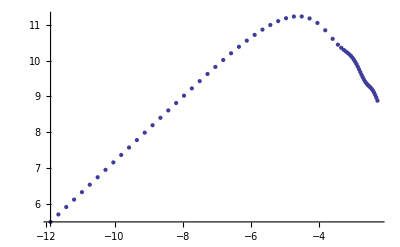

```mathematica
Transpose@{CLASS["kvalues"]/.cl,CLASS["linearPk"]/.cl}//ListPlot
```